## Set up

```mathematica
alpha=2;
l=16;
hd="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[hd,"2_16_DEN_var_ldas"];
SetDirectory[wd];
```

```mathematica
nrep=3;
nprop=13;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
wt=ConstantArray[0,l];
AA={"A","C","G","T"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences;
wtAA = sequencesAA[[1]];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
L=MakeLapRec[alpha,l];//AbsoluteTiming
```

{6.89639,Null}

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

#### Export design matrix for glmnet

```mathematica
(*varall = ConstantArray[0, alpha^l];*)
```

```mathematica
(*designAllonehot=s2donehot[sequences,Range[0,l]];//AbsoluteTiming*)
```

```mathematica
(*rules=Flatten[Table[Join[Table[designrules[sequences[[j]],k,wt,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,3}]}];
Export["data/rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];*)
```

## *Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, Correlation[x, y]^2];


mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

### Regression functions

```mathematica
(*Ridge regression with regularization parameter "Î»" and design matrix "design"*)

RidgeRegression[design_, response_, Î»_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += Î»^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2dTaylor2[seqs_,order_,wt_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrules[seqs[[j]],k,wt,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,order}]}]]
```

### Kernelized regressions

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2](*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1](*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]
```

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[{Ai,Ab},Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y](*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]]

(*10-fold crossvalidation using the function Creg*)CrossvalidationC[Ccoeffs_,Pcoeffs_,list_,response_,rps_,variance_,fold_,rep_]:=Module[{size,subsets,r,rpsr},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];r=Table[Table[{},Length[rps]+1],rep];Do[Do[r[[k]][[i+1]]=Creg[Ccoeffs,Pcoeffs,list[[Flatten[Drop[subsets,{k}]]]],response[[Flatten[Drop[subsets,{k}]]]],rps[[i]],variance[[Flatten[Drop[subsets,{k}]]]],{}],{i,Length[rps]}],{k,rep}];Table[mse[r[[k]][[i+1]][[list[[subsets[[k]]]]]],response[[subsets[[k]]]]]
,{k,rep},{i,Length[rps]}]
]

(*Extract best regularization parameter from the crossvalidation outputs*)CV[mse_,rps_]:=Module[{means,ses,min,bestlambda},means=Mean[mse];ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];min=First[Ordering[means]];bestlambda=rps[[min ]];{bestlambda,means,ses}]
```

### Matrix coefficients

```mathematica
(*Krawtchouk polynomial*)
w[alpha_, k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[alpha,k,d],{d,0,l},{k,0,l}];
```

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

### Build matrices

```mathematica
(*(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[Join[ParallelTable[{i,i}->l(A-1),{i,1,A^l}],Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]*)
```

```mathematica
(*AbsoluteTiming[L=MakeLaplacian[alpha,l];]*)
```

```mathematica
(*MakeAdj[A_,l_]:=SparseArray[Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]*)
```

```mathematica
(*Adj=MakeAdj[alpha,l];//AbsoluteTiming*)
```

```mathematica
(*Adj = -(L - SparseArray[Flatten[Table[{i,i}->(alpha-1)*l,{i,1,alpha^l}],2]]);*)
```

```mathematica
(*null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];//AbsoluteTiming*)
```

```mathematica
(*null2=SparseArray[Table[Join[s2dTaylor[seq,0,wt],s2dTaylor[seq,1,wt],s2dTaylor[seq,2,wt]],{seq,sequences}]];//AbsoluteTiming*)
```

```mathematica
designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,0, 1}]],{j,Length[sequences]}],2];//AbsoluteTiming
```

{8.7286,Null}

```mathematica
nullonehot=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha)^k,{k,0,1}]}];
```

## Simulate

### Well defined random field with exponential lambdas

```mathematica
blist={3,2.5,2,1.5, 1,0.75,.5};
```

```mathematica
lambdaslist=Table[Nbyfirst@Table[Exp[-b*k],{k,1,l}],{b,blist}];
```

```mathematica
lambdas1h=Nbyfirst@Table[2^(l-i) (1 + (alpha-1)*.5)^(l-i),{i,1,l}]
```

{1.,0.333333,0.111111,0.037037,0.0123457,0.00411523,0.00137174,0.000457247,0.000152416,0.0000508053,0.0000169351,5.64503×10^-6,1.88168×10^-6,6.27225×10^-7,2.09075×10^-7,6.96917×10^-8}

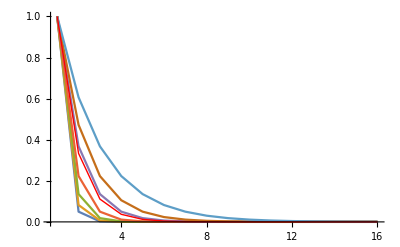

```mathematica
Show[ListLinePlot[lambdaslist,PlotRange->All],
ListLinePlot[lambdas,PlotStyle->{Red,Thick},PlotRange->All]]
```

```mathematica
Do[Export[StringJoin["data/tru_lda_",ToString[blist[[i]]],".tsv"],lambdaslist[[i]]//N],{i,Length@blist}];
```

```mathematica
VC1h=Nbysum[Rest@mks*lambdas1h];
```

```mathematica
VClist=Table[Nbysum[Rest@mks*lambdaslist[[i]]],{i,Length@blist}]//N;
```

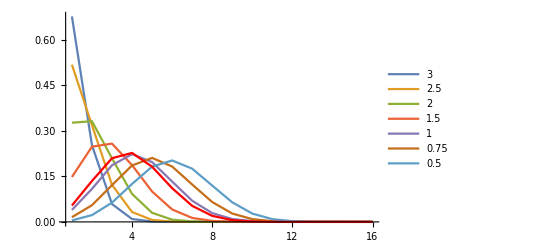

```mathematica
Show[ListLinePlot[VClist,PlotRange->All,PlotLegends->blist],
ListLinePlot[VC1h,PlotRange->All,PlotStyle->{Red,Thick}]
]
```

```mathematica
rholist=Table[Nbyfirst[wkd[[All,2;;]].lda],{lda,lambdaslist}]//N;
```

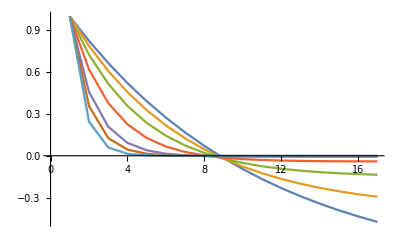

```mathematica
ListLinePlot[rholist]
```

```mathematica
Export[StringJoin["data/",fl,"_lambdas",".tsv"], lambdas];
```

```mathematica
fslist=Table[{},Length@blist,nrep];
```

```mathematica
Do[
f=RandomVariate[NormalDistribution[],alpha^l];f=Table[Sqrt[(lambdaslist[[j]][[k]]mks[[k+1]]/Norm[Pkby[f,k]]^2)]Pkby[f,k],{k,1,l}]//Total;
fslist[[j,i]]=f,
{j,Length@blist},
{i, nrep}]
```

```mathematica
Do[fslist[[j,i]]=fslist[[j,i]]/StandardDeviation[fslist[[j,i]]],{j,Length@blist},{i, nrep}]
```

```mathematica
Table[Round[Table[Norm[Pkby[fslist[[j,i]],k]]^2/mks[[k+1]],{k,1,l}]-lambdaslist[[j]],10^7],{j,Length@blist},{i,nrep}]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Do[Export[StringJoin["data/",StringRiffle[{fl,"f",ToString[blist[[j]]],ToString[i]},"_"],".tsv"],fslist[[j,i]],"TSV"],{j,Length@blist},{i,nrep}]
```

## Generate training samples

### Random sampling

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
trs=Table[RandomSample[Range[Length[sequences]],samplesizes[[i]]],{i,Length[samplesizes]}];
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
Do[Export[StringJoin[ "data/", "tr_",ToString[i],".tsv"],trs[[i]],"TSV"],{i,lg@trs}];
```

### Simulated mutagenesis

```mathematica
wt=ConstantArray[0,l];
```

```mathematica
wg=mks^(-1)//N
```

{1.,0.0625,0.00833333,0.00178571,0.000549451,0.000228938,0.000124875,0.0000874126,0.0000777001,0.0000874126,0.000124875,0.000228938,0.000549451,0.00178571,0.00833333,0.0625,1.}

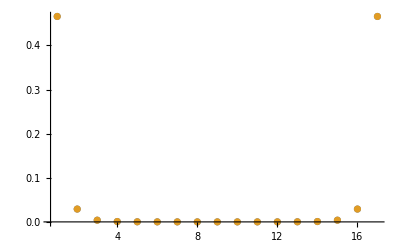

```mathematica
ListPlot[{Nbysum[mks^-1],Nbysum[wg]},PlotRange->All]
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
p=.1;
weights=(1-p)^(-#+l) p^# &/@hd;
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
trsmut=Table[RandomSample[weights->Range[alpha^l],Ceiling[i alpha^l]],{i,proportions}];
tstmut=Table[Complement[Range[alpha^l],trsmut[[i]]]//Flatten,{i,Length[proportions]}];
```

```mathematica
proportions//N
```

{0.00999451,0.0500031,0.100006,0.199997,0.300003,0.399994,0.5,0.600006,0.699997,0.800003,0.899994,0.949997,0.990005}

```mathematica
SortBy[hd[[trsmut[[1]]]]//Tally,First]
%[[All,2]]/mks[[;;Length[%]]]//N
```

{{0,1},{1,16},{2,120},{3,308},{4,153},{5,48},{6,6},{7,1},{8,2}}

{1.,1.,1.,0.55,0.0840659,0.010989,0.000749251,0.0000874126,0.0001554}

```mathematica
Do[Export[StringJoin["data/", "tr_mut_",ToString[i],".tsv"],trsmut[[i]],"TSV"],{i,lg@trsmut}];
```

## Make figures

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
fl="2_16_DEN";
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fslist=Table[{},Length@blist,nrep];
```

```mathematica
Do[
fslist[[j,i]]=Import[StringJoin["data/",StringRiffle[{fl,"f",ToString[blist[[j]]],ToString[i]},"_"],".tsv"]]//Flatten,{j,Length@blist},{i,nrep},
{j,Length@blist},
{i, nrep}];
```

### Import training samples

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
modelname="vc";
scheme="mut";
```

```mathematica
pdsVCmut=Table[{}, Length@blist, nrep];
Do[name=StringRiffle[{fl,scheme,"vc",ToString[blist[[k]]],ToString[i],ToString[2]},"_"];
pdsVCmut[[k,i]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,Length@blist},{i,nrep}
]
```

```mathematica
pdsVCmut[[3,1]]
```

{}

```mathematica
blist[[3]]
```

2

```mathematica
k=3;
i=1;
```

```mathematica
name
```

2_16_DEN_mut_vc_2_1_2

```mathematica
mseVCmut=Table[mse[fslist[[k,i]][[tstbyD[[d]]]], pdsVCmut[[k,i]][[tstbyD[[d]]]]],{k,Length@blist},{d,l+1},{i,nrep}];
```

```mathematica
input=mseVCmut[[1]];
```

```mathematica
plotdat=Table[{Around[d,0],Around[Mean[input[[d+1]]],
.5StandardDeviation[input[[d+1]]]]},{d,dmin,l}]
```

{{4,0.0060.005},{5,0.0170.014},{6,0.0340.028},{7,0.050.04},{8,0.120.09},{9,0.150.11},{10,0.280.21},{11,0.330.22},{12,0.50.4},{13,0.470.27},{14,0.70.5},{15,0.360.17},{16,0.310.25}}

### Plotting functions

```mathematica
MSEbyD[input_]:=Module[{},
plotdat=Table[{Around[d,0],Around[Mean[input[[d+1]]],
.5StandardDeviation[input[[d+1]]]]},{d,dmin,l}];
Show[ListLogPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
(*Adjust Plot Range*)
PlotRange->{{0,l+.2},{.01, 80}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Automatic,False},{Range[0,l],False}},FrameLabel->{"Hamming Distance to WT","Scaled out-of-sample MSE"},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],legpos],
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1}
]]
]
```

```mathematica
summaryfig3[lambdas_,lambdaspos_,  alpha_, l_]:=Module[
{},
wkd = Table[w[alpha,l, k,d],{d,0,l},{k,0,l}];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
(*rho prior*)
rho = wkd[[All,2;;]].Rest[lambdas];
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",ToString[ρ]},
FrameTicks->{{Range[-.5,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->{GrayLevel[.5], thicksum},
BaseStyle->{FontSize->fontsize},
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.2},{-.5,1}},
PlotRangeClipping->False
],
ListPlot[
plotdat,
PlotRange->All,
PlotStyle->{Gray}
]
];
(*rho posterior*)
rhopos = Table[Nbyfirst[wkd[[All,2;;]].Rest[lambdaspos[[i]]]],{i,Length[lambdaspos]}];
plotdat=errorplotdat[rhopos];
figrhopos = Show[ListPlot[plotdat,DataRange->{0,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False]];
(*vc prior*)
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdas*Rest@multiplicities]};
figvcBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.7],
ImageSize->400,
PlotRange->{{.5,l+.5},All},
PlotRangeClipping->False,
AspectRatio->.75
];
(*vc posterior*)
vcpos = Table[Nbysum[Rest@lambdaspos[[i]]*Rest@multiplicities],{i,Length[lambdaspos]}];
plotdat = errorplotdat[vcpos];
figvcpos = Show[ListPlot[plotdat,DataRange->{1,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],ListLinePlot[plotdat[[All,1]],DataRange->{1,l},PlotRange->All,PlotStyle->{GrayLevel[.25],thicksum}]];
(*Gamma Prior*)
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
gammak=Table[(mk[[k]].wkd.lambdas),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
gammak=Table[(mk[[k]].rho),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
k=1;
figgamma=Table[Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k+1]]]-1],Nbyfirst[gammak[[k+1]]]};
Show[
ListLinePlot[
plotdat,
Frame->True,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},
FrameTicks->{{Range[0,2,.2]/.{0.->0,1.->1},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->{GrayLevel[.5], thicksum},
ImageSize->400,
AspectRatio->.75,
FrameStyle->fstyle,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False],
ListPlot[
plotdat,
PlotStyle->{Gray}]]
],{k,0,3}];
(*Gamma posterior*)
gamma1pos=Table[Most[mk[[2]].rhopos[[i]]],{i,Length[rhopos]}];
gamma1pos = Nbyfirst/@gamma1pos;
plotdat = errorplotdat[gamma1pos];
figgamma1pos = Show[ListPlot[plotdat,DataRange->{0,l-1},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l-1},PlotRange->All,PlotStyle->{GrayLevel[.25], thicksum}]];

{Show[figrho,figrhopos],Show[figvcBar,figvcpos],Show[figgamma[[2]],figgamma1pos]}
]
```

### Plotting

```mathematica
vcsAll=Table[Transpose@{Range[l],Nbysum[Rest@mks*lambdaslist[[i]]]},{i,Length@blist}]//N;
```

```mathematica
lambdasest=Table[{},Length@blist,nrep];
```

```mathematica
Do[
lambdasest[[j,i]]=Import[StringJoin["data/",StringRiffle[{fl,"f",ToString[blist[[j]]],ToString[i]},"_"],".tsv"]]//Flatten,{j,Length@blist},{i,nrep},
{j,Length@blist},
{i, nrep}];
```

$Aborted

```mathematica
lambdasest=Table[]
```

```mathematica
plots=Table[GraphicsColumn[Join[summaryfig3[PadLeft[lambdaslist[[i]],17],Table[PadLeft[lambdaslist[[i]],17] + RandomVariate[NormalDistribution[0,10^-7],17],10],  2, 16][[;;2]],{MSEbyD[mseVCmut[[i]]]}],ImageSize->400,Spacings->.5],{i,Length@blist}];
```

```mathematica
plot1h=GraphicsColumn[Join[summaryfig3[PadLeft[lambdas,17],Table[PadLeft[lambdas,17] + RandomVariate[NormalDistribution[0,10^-7],17],10],  2, 16][[;;2]],{MSEbyD[results[[3,2,3,1]]]}],ImageSize->400,Spacings->.5];
plot1hlabed=Labeled[plot1h,MaTeX[StringInsert["\\lambda_k = e^{-k}",ToString[-Round[Log[lambdas][[2]],.01]],17],FontSize->20],Top];
```

```mathematica
plotslabed=Table[Labeled[plots[[i]],MaTeX[StringInsert["\\lambda_k = e^{-k}",ToString[blist[[i]]],17],FontSize->20],Top],{i,Length@blist}];
```

```mathematica
plotsAllPanels=Insert[plotslabed,plot1hlabed,6];
```

```mathematica
Export["fig_varying_ldas.pdf",Grid[{plotsAllPanels}]]
```

fig_varying_ldas.pdf

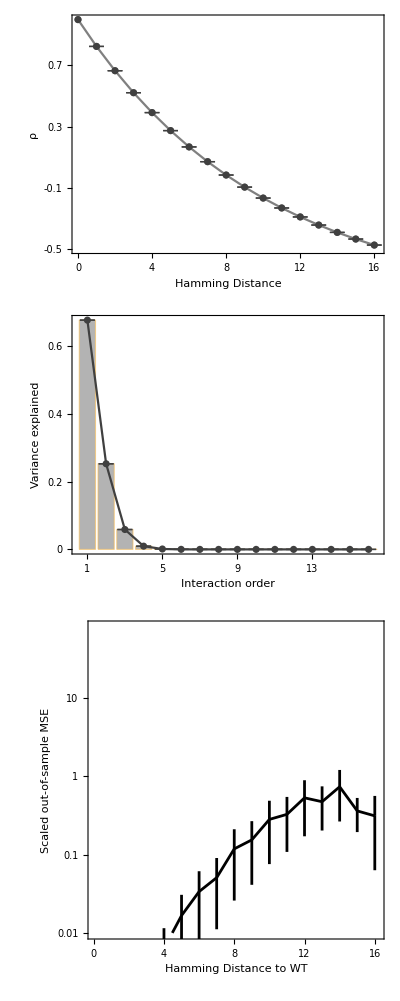
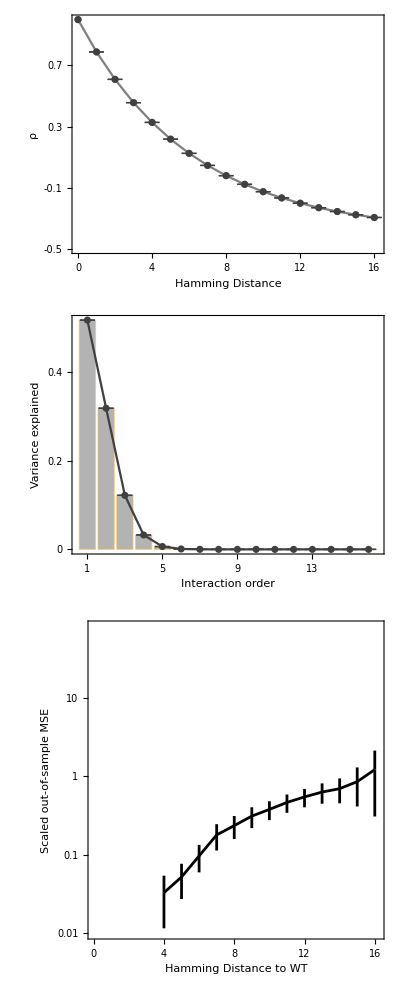
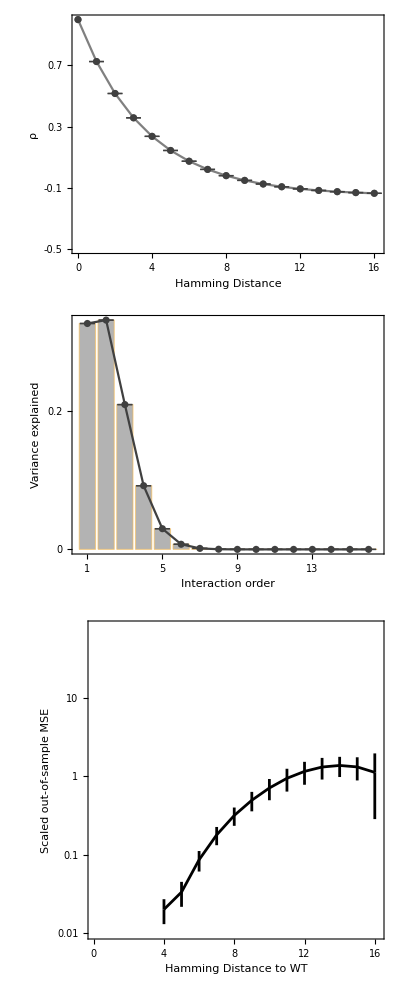
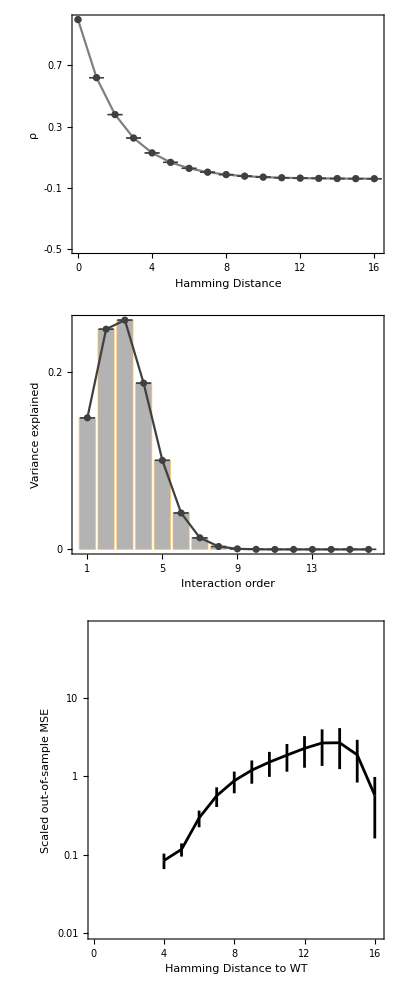
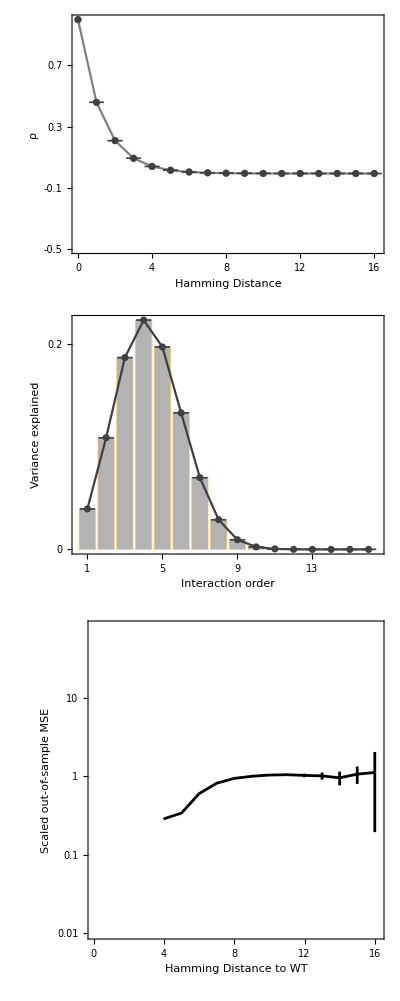
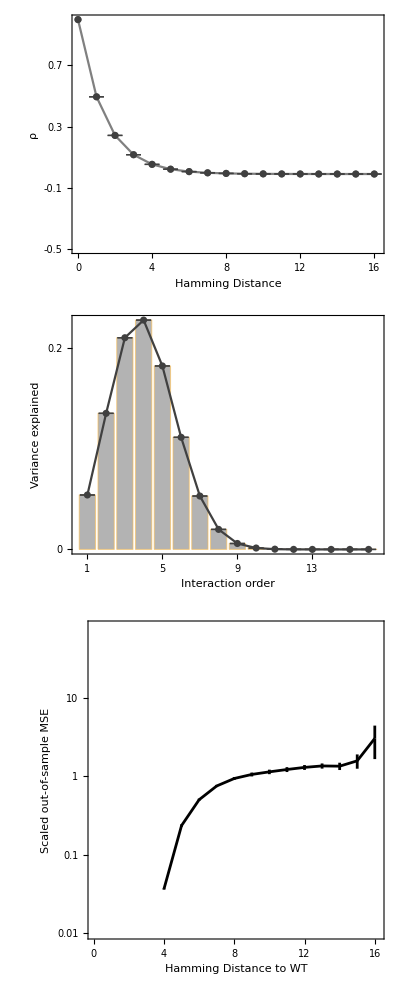
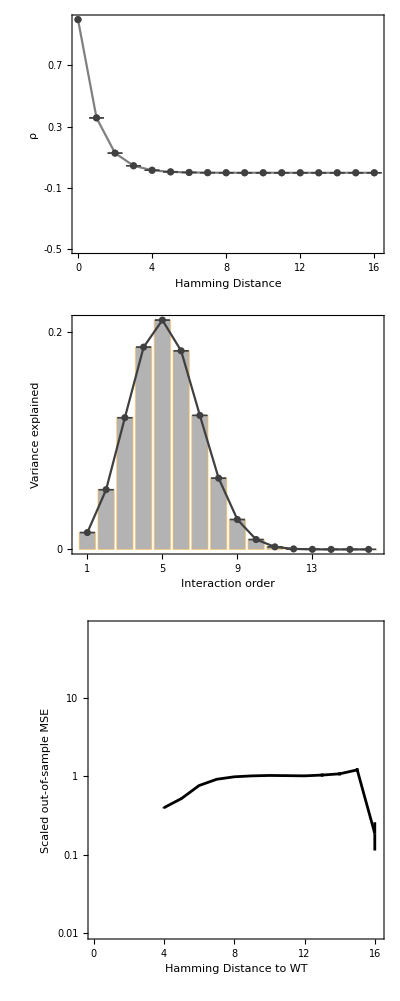
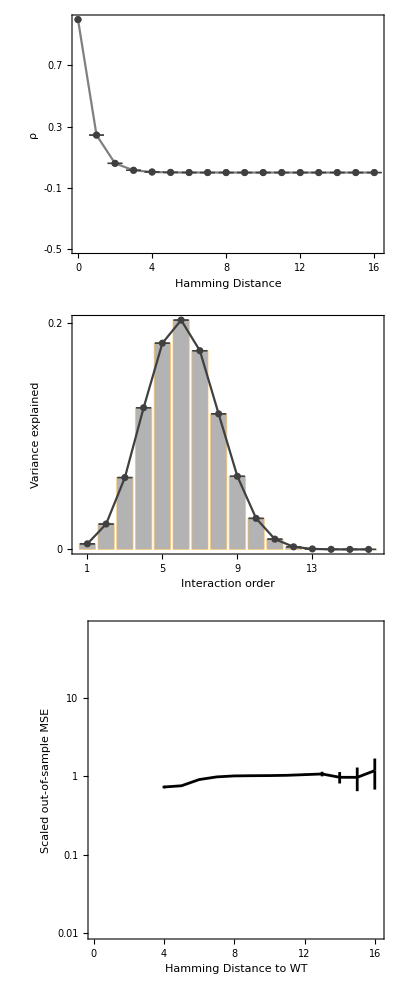
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Grid[{plotsAllPanels}]
```

```mathematica
R2VCmut=Table[r2[fslist[[k,i]][[Complement[Range[alpha^l],trsmut[[i]]]]], pdsVCmut[[k,i]][[Complement[Range[alpha^l],trsmut[[i]]]]]],{k,Length@blist},{i,nrep}];
```

```mathematica
TableForm[Round[R2VCmut,.01],TableHeadings->{blist, None}]
```

3 | 0.98 | 0.98 | 0.7
2.5 | 0.7 | 0.92 | 0.67
2 | 0.77 | 0.7 | 0.34
1.5 | 0.39 | 0.17 | 0.45
1 | 0.18 | 0.14 | 0.14
0.75 | 0.1 | 0.09 | 0.08
0.5 | 0.06 | 0.03 | 0.03

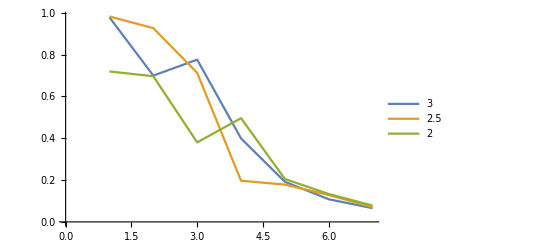

```mathematica
ListLinePlot[R2VCmut//Transpose,PlotLegends->blist]
```

```mathematica
Grid[{plotsAllPanels[[{1,3,6}]]}]
```

-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

Horizontal design
nrep = 10
lambdas, one, twice and three times -1.1